# Simple Task 8 Valerie Richmond 2/26/14

```mathematica
1.
    a. The explanation is incorrect because f2[x]is not only positive between 480 and 520. It is also positive around 500000. The NSolve function misses the third zero because it uses Newton's Method, and the starting guess is too far off for the method to find the zero around 500000. Solve, on the other hand, uses other methods to find solutions. The explanation is also wrong because it does not realize that the function f2 is cubic within the square root, so the behavior of the two ends must go in opposite directions.

b.
```

```mathematica
g2[x_] := 3 Sin[ x/3] + 5
f2[x_] := √(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)
```

```mathematica
FindRoot[√(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)==3 Sin[ x/3] + 5, {x,485}]
FindRoot[√(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)==3 Sin[ x/3] + 5, {x,490}]
FindRoot[√(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)==3 Sin[ x/3] + 5, {x,500}]
FindRoot[√(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)==3 Sin[ x/3] + 5, {x,510}]
FindRoot[√(9.384*^-8 x^3+ -0.047 x^2+ 46.75 x + -11621.62)==3 Sin[ x/3] + 5, {x,500000}]
```

{x→483.816}

{x→488.256}

{x→500.673}

{x→507.218}

{x→499856.}

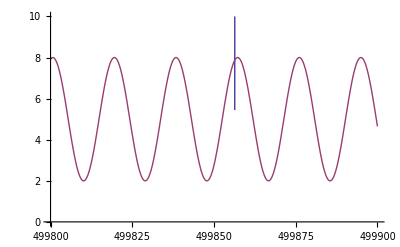

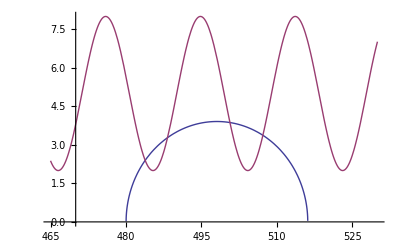

```mathematica
Plot[{f2[x],g2[x]},{x, 499800,499900}, PlotRange->{0,10}]
Plot[{f2[x],g2[x]},{x, 465, 530}, PlotRange->{0,8}]
```

c. These graphs show all of the intersections since the function within the square root is cubic and the leading coefficient is positive. So, the y function values must go to negative infinity as x does and must go to positive infinity as x does. The graphs show the three regions where one graph passes through the y-range of the second bounded sin graph. The sin graph will stay within its bound between 2 and 8 while the cubic will shoot off away from the range.

2.

a. The problem is caused by an unlisted local variable. In the testMe module, i is used as the incrementor and in the continuation condition, but it is not listed in the local variables list. So, Mathematica assumed that i was a global variable instead of using it to refer to a unique value within the function.

b.

```mathematica
(* testMe creates and returns a list with the squares of all the integer values
from start to stop (inclusive). We assume start and stop are integers. Each element of the list is of the form {x,x^2} where start≤x≤stop.*)
testMe[start_, stop_] := Module[{reslst={},i(*Change here!*)},
For[ i=start, i≤ stop, i++,
      reslst =  Append[reslst, {i, square[i]}];
];
Return[reslst]
]
```

```mathematica
(* square computes the sum of all the odd numbers up to 2 x (exclusive). This is a complicated way of computing x^2- but it works. You are not allowed to 
change the algorithm to fix the problem. *)
square[x_ ] := 
Module[{sum=0},
For[i=1,i<2x, i= i+2, 
sum= sum+ i
];
Return[sum]
]
```

```mathematica
testMe[7,22]
```

{{7,49},{8,64},{9,81},{10,100},{11,121},{12,144},{13,169},{14,196},{15,225},{16,256},{17,289},{18,324},{19,361},{20,400},{21,441},{22,484}}

```mathematica
testMe[0, 10]
```

{{0,0},{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}